```mathematica
(* 01 *)
ExampleData[]
```

{AerialImage,Audio,ColorTexture,Dataset,Geometry3D,LinearOptimization,LinearProgramming,MachineLearning,Matrix,NetworkGraph,Sound,SpatialPointData,Statistics,TestAnimation,TestImage,TestImage3D,TestImageSet,Text,Texture}

```mathematica
(* 02 *)
ExampleData[{"Matrix","1138BUS"}] (* 在数据集中检索1138BUS的方法 *)
```

SparseArray[…]

```mathematica
(* 03 *)
```

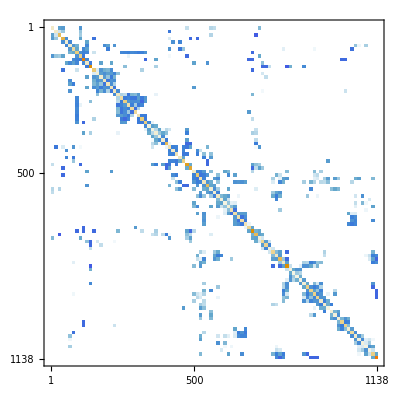

```mathematica
MatrixPlot[%2]
```

```mathematica
(* 04 *)
testdata19 = Import["https://www.handsonstart.com/HOS-Chapter19-1.xlsx"];
```

```mathematica
(* 05 *)
```

```mathematica
Dimensions[testdata19]
```

{1,125,25}

```mathematica
(* 06 *)
testimage19 = Import["https://www.handsonstart.com/HOS-Chapter19-2.jpg"];
```

```mathematica
(* 07 *)
ImageSize[testimage19]
```

ImageSize[-Graphics-]

```mathematica
(* 08 *)
SemanticImport["http://www.handsonstart.com/HOS-Chapter19-3.csv"]
```

```mathematica
Dataset[%10,DatasetTheme->"Business"]
```

```mathematica
Normal[%10]
```

{{Shanghai,14010000},{Istanbul,13300000},{Tokyo,13300000},{Mumbai,12690000},{Beijing,12460000},{Zhoukou,12070000},{Dhaka,11880000},{Nanyang,11680000},{Karachi,11620000},{Baoding,11550000},{Chengdu,11400000},{Delhi,10930000},{São Paulo,10660000},{Moscow,10560000},{Linyi,10420000},{Jakarta,10190000},{Harbin,9916000},{Tianjin,9798000},{Shijiazhuang,9774000},{Seoul,9708000},{Xuzhou,9576000},{Handan,9428000},{Heze,9394000},{Cairo,9120000},{Shangqiu,9109000}}

```mathematica
(* 09 *)
Entity["City",{"Shanghai","Shanghai","China"}]
```

Shanghai

```mathematica
CityData[Entity["City",{"Shanghai","Shanghai","China"}],"Longitude"]
```

121.47 °

```mathematica
CityData[Entity["City",{"Shanghai","Shanghai","China"}],"Latitude"]
```

31.23 °

```mathematica
(* 10 *)
```

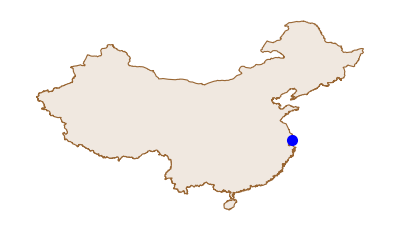

```mathematica
"位置"Entity["City",{"Shanghai","Shanghai","China"}]Show[Graphics[{EdgeForm[Brown],LightBrown,CountryData["China","Polygon"],Blue,PointSize[0.02],Point[Reverse[CityData[Entity["City",{"Shanghai","Shanghai","China"}],"Coordinates"]]]}]]
```